```mathematica
TableForm[
Sort[
Table[
With[
{
g=EmbedGraphInPlantri8[ allGraphs5,k]
},
{
EdgeCount[g],
ChromaticPolynomial[g,4],
VertexCount[g],
EdgeCount[g]==VertexCount[g]*3-6,
EdgeCount[g]-(VertexCount[g]*3-6),
VertexCount[g]*3-6,
ShowGraph5Least[k],
PlanarGraphQ[g]
}
],{k,allGraphs5AtomKeys}],
#1[[5]]<#2[[5]]&
],TableHeadings->{None, {"edge","chrom","vertex","edge==3v-6","edge⩾3v-6","3v-6","graph","planar"}}
]
```

edge | chrom | vertex | edge==3v-6 | edge⩾3v-6 | 3v-6 | graph | planar
30 | 384 | 12 | True | 0 | 30 | -Graphics-590481 | True
33 | 384 | 13 | True | 0 | 33 | -Graphics-582881 | True
33 | 432 | 13 | True | 0 | 33 | -Graphics-567701 | True
33 | 288 | 13 | True | 0 | 33 | -Graphics-560121 | True
36 | 480 | 14 | True | 0 | 36 | -Graphics-560111 | True
33 | 432 | 13 | True | 0 | 33 | -Graphics-522321 | True
33 | 624 | 13 | True | 0 | 33 | -Graphics-499721 | True
36 | 504 | 14 | True | 0 | 36 | -Graphics-499631 | True
33 | 264 | 13 | True | 0 | 33 | -Graphics-492201 | True
36 | 696 | 14 | True | 0 | 36 | -Graphics-492161 | True
36 | 384 | 14 | True | 0 | 36 | -Graphics-492081 | True
33 | 384 | 13 | True | 0 | 33 | -Graphics-390141 | True
33 | 288 | 13 | True | 0 | 33 | -Graphics-326841 | True
36 | 480 | 14 | True | 0 | 36 | -Graphics-324411 | True
33 | 264 | 13 | True | 0 | 33 | -Graphics-305861 | True
36 | 384 | 14 | True | 0 | 36 | -Graphics-304961 | True
36 | 696 | 14 | True | 0 | 36 | -Graphics-302621 | True
33 | 264 | 13 | True | 0 | 33 | -Graphics-298881 | True
36 | 336 | 14 | True | 0 | 36 | -Graphics-298571 | True
36 | 336 | 14 | True | 0 | 36 | -Graphics-297681 | True
36 | 336 | 14 | True | 0 | 36 | -Graphics-295371 | True
37 | 312 | 14 | False | 1 | 36 | -Graphics-514750 | False
37 | 192 | 14 | False | 1 | 36 | -Graphics-492100 | False
40 | 264 | 15 | False | 1 | 39 | -Graphics-492070 | False
37 | 168 | 14 | False | 1 | 36 | -Graphics-382810 | False
37 | 312 | 14 | False | 1 | 36 | -Graphics-368170 | False
37 | 192 | 14 | False | 1 | 36 | -Graphics-360860 | False
37 | 192 | 14 | False | 1 | 36 | -Graphics-319540 | False
37 | 192 | 14 | False | 1 | 36 | -Graphics-303340 | False
40 | 264 | 15 | False | 1 | 39 | -Graphics-302530 | False
37 | 240 | 14 | False | 1 | 36 | -Graphics-297970 | False
40 | 240 | 15 | False | 1 | 39 | -Graphics-297670 | False
37 | 240 | 14 | False | 1 | 36 | -Graphics-296330 | False
37 | 744 | 14 | False | 1 | 36 | -Graphics-295600 | False
40 | 480 | 15 | False | 1 | 39 | -Graphics-295330 | False
40 | 240 | 15 | False | 1 | 39 | -Graphics-295250 | False
35 | 120 | 13 | False | 2 | 33 | -Graphics-514780 | False
35 | 216 | 13 | False | 2 | 33 | -Graphics-383080 | False
35 | 120 | 13 | False | 2 | 33 | -Graphics-368980 | False
35 | 96 | 13 | False | 2 | 33 | -Graphics-361940 | False
38 | 72 | 14 | False | 2 | 36 | -Graphics-361660 | False
38 | 192 | 14 | False | 2 | 36 | -Graphics-361120 | False
41 | 216 | 15 | False | 2 | 39 | -Graphics-360850 | False
35 | 96 | 13 | False | 2 | 33 | -Graphics-319840 | False
38 | 192 | 14 | False | 2 | 36 | -Graphics-317380 | False
38 | 72 | 14 | False | 2 | 36 | -Graphics-317140 | False
41 | 216 | 15 | False | 2 | 39 | -Graphics-317110 | False
38 | 0 | 14 | False | 2 | 36 | -Graphics-296080 | False
41 | 144 | 15 | False | 2 | 39 | -Graphics-296050 | False
41 | 264 | 15 | False | 2 | 39 | -Graphics-295510 | False
41 | 144 | 15 | False | 2 | 39 | -Graphics-295270 | False
45 | 0 | 16 | False | 3 | 42 | -Graphics-295240 | False

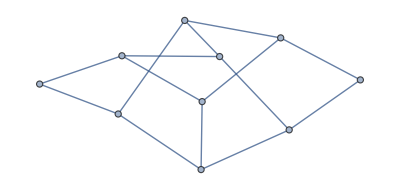
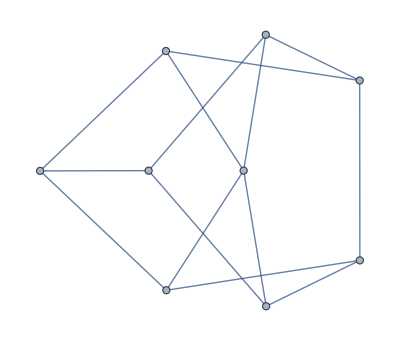

```mathematica
Map[Graph[EdgeList[#]]&,SimpleMinors[PetersenGraph[]]]
```

```mathematica
MMNCGraphQ [PetersenGraph[]]
```

False

```mathematica
SimpleMinors[plantri8]
```

28